```mathematica
Needs["PlotLegends`"]
```

```mathematica
NN = 3
```

3

```mathematica
σ[m_, p_] := - Power[Abs[m^NN] - 1., 1/NN] ⅇ^(2 π ⅈ  (p ) / NN)
```

```mathematica
M[m_,k_] := m ⅇ^(2 π ⅈ k / NN)
```

```mathematica
W[m_, p_] := - NN σ[m, p ]  -
    ( m Log[ σ[m,p] - m ]  +
  M[m,1] Log[ σ[m,p] - M[m,1] ] + 
  M[m,2] Log[σ[m,p] - M[m,2] ] )
```

```mathematica
W[5.,0]  // N
```

-6.62374-15.708 ⅈ

```mathematica
F[m_] := (W[m,1] - W[m,0])/(M[m,1] - M[m,0])
```

```mathematica
R = π/(2 √3) + 3/2 Log[3.]  - 3.0
```

-0.445182

```mathematica
σ[-10., 0]
```

-9.99667

```mathematica
Asympt[m_] := R + 3 Log [ Abs[m]]
```

```mathematica
Plot[{ Re[F[m] // N], Asympt[m]}, {m, -100., -1}, PlotStyle->{{Thick,Blue},{Thickness[0.006],Purple, Dashing[0.03]}},
AxesLabel->{Style["m_0" , FontSize->15],Style["(W (SubscriptBox[σ, 1]) - W (SubscriptBox[σ, 0]))/m_1",FontSize->15]}, 
PlotLegend->{Style["numeric",FontSize->15],Style["3 ln|m_0| + R",FontSize->15]},LabelStyle->Directive[FontSize->15]]
```

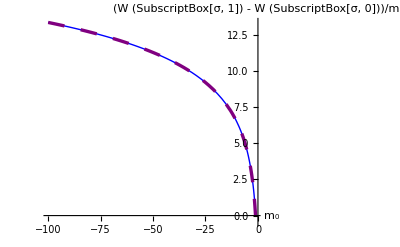

```mathematica
Plot[{ Re[F[m] // N], Asympt[m]}, {m, -10, -1}, PlotStyle->{{Thick,Blue},{Thickness[0.006],Purple, Dashing[0.03]}},
AxesLabel->{Style["m_0" , FontSize->15],Style["(W (SubscriptBox[σ, 1]) - W (SubscriptBox[σ, 0]))/m_1",FontSize->15]}, 
PlotLegend->{Style["numeric",FontSize->15],Style["3 ln|m_0| + R",FontSize->15]}, LabelStyle->Directive[FontSize->15],PlotRange->{{-10,0}}]
```

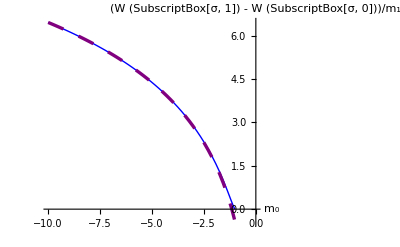

```mathematica
W[-1,0]
```

-3.6276+0. ⅈ

```mathematica
- 2 π/(√3) // N
```

-3.6276

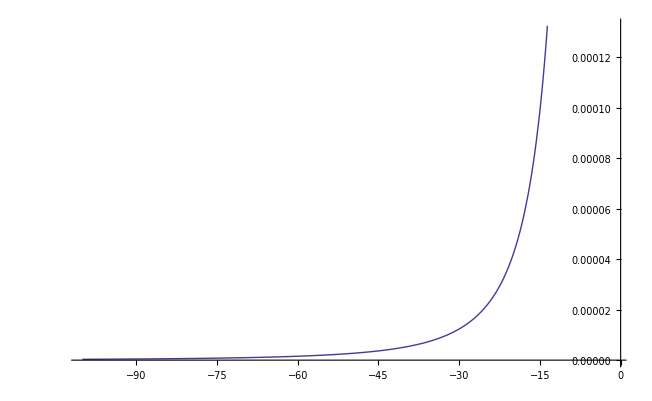

```mathematica
Plot[{ Re[F[m]] - R - 3 Log [ Abs[m]]}, {m, -100., -1} ]
```

```mathematica
H[m_] :=  Re[F[m]] - R - 3 Log [ Abs[m]]
```

```mathematica
H[-2.]
```

0.0425776

```mathematica
H[-10.]
```

0.000333389

```mathematica
H[-100.]
```

3.32358×10^-7

```mathematica
H[-1000.]
```

-1.027×10^-6

```mathematica
G[m_] := (W[m,1] - ⅇ^(2π ⅈ/NN) W[m,0])/(2 π ⅈ M[m,2])
```

```mathematica
G[-30]
```

1.+2.36303×10^-13 ⅈ

```mathematica
G[-40]
```

1.-2.857×10^-12 ⅈ

```mathematica
G[-100]
```

1.-1.72252×10^-11 ⅈ